```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#,"graph"],CompleteGraph[4]]&]}]
```

{-Graphics-29525,-Graphics-29527,-Graphics-29533,-Graphics-29551,-Graphics-29605,-Graphics-29767,-Graphics-30253,-Graphics-31711,-Graphics-36085,-Graphics-49207}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#,"graph"],CompleteGraph[3]]&]}]
```

{-Graphics-29537,-Graphics-29560,-Graphics-29608,-Graphics-29633,-Graphics-29768,-Graphics-29797,-Graphics-29857,-Graphics-30262,-Graphics-30334,-Graphics-30496,-Graphics-31714,-Graphics-31738,-Graphics-31954,-Graphics-32441,-Graphics-36086,-Graphics-36112,-Graphics-36166,-Graphics-36817,-Graphics-38281,-Graphics-49208,-Graphics-49210,-Graphics-49216,-Graphics-49963,-Graphics-51475,-Graphics-56011}

```mathematica
MobiusGraphDoubleGood5[29551,31738,allGraphs5]
```

MobiusGraphDoubleGood5[29551,31738,<|0→<|signature→0,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,11,colofournull→p1x2x3x4x5,colofourrealnull→n1x2x3x4x5|>,19683→<|signature→19683,matrix→{{2,1,0,0,0},{1,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,11,colofournull→p12x3x4x5,colofourrealnull→-n12x3x4x5+n1x2x3x4x5|>,1891,1→<|signature→1,14,colofourrealnull→1|>,2→<|signature→2,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,2},{0,0,0,2,2}},graph→-Graphics-,11,colofournull→-p1x2x3x45+p1x2x3x4x5,colofourrealnull→n1x2x3x45|>|>]
 |  |  |  |

```mathematica
MobiusGraphDoubleGood5[29551,36112,allGraphs5]
```

MobiusGraphDoubleGood5[29551,36112,<|0→<|signature→0,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,11,colofournull→p1x2x3x4x5,colofourrealnull→n1x2x3x4x5|>,19683→<|signature→19683,matrix→{{2,1,0,0,0},{1,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,11,colofournull→p12x3x4x5,colofourrealnull→-n12x3x4x5+n1x2x3x4x5|>,1891,1→<|signature→1,14,colofourrealnull→1|>,2→<|signature→2,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,2},{0,0,0,2,2}},graph→-Graphics-,11,colofournull→-p1x2x3x45+p1x2x3x4x5,colofourrealnull→n1x2x3x45|>|>]
 |  |  |  |

```mathematica
allGraphs5[36112,"colofourrealnull"]
```

2 n12345-n1235x4-n134x25-n13x245+n13x25x4

```mathematica
Reduce[2 n12345-n1235x4-n134x25-n13x245+n13x25x4==0]
```

n12345==n1235x4/2+n134x25/2+n13x245/2-n13x25x4/2

```mathematica
allGraphs5[29551,"colofourrealnull"]
```

-6 n12345+2 n1235x4+2 n1245x3+n125x34-n125x3x4+2 n134x25+n13x245-n13x25x4+n14x235-n14x25x3+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4

```mathematica
allGraphs5[29551,"colofourrealnull"]/.n12345->n1235x4/2+n134x25/2+n13x245/2-n13x25x4/2//Simplify
```

-n1235x4+2 n1245x3+n125x34-n125x3x4-n134x25-2 n13x245+2 n13x25x4+n14x235-n14x25x3+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4

```mathematica
SummaryPrintGood5[36112]
```

SummaryPrintGood5[36112]

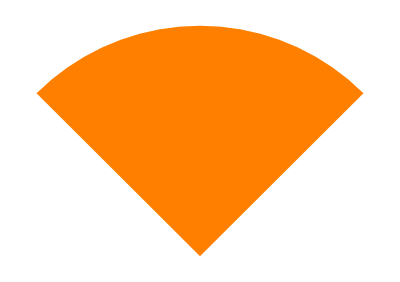

```mathematica
Graphics[{Orange,Disk[{0,0},1,{Pi/4,3 Pi/4}]}]
```

```mathematica
MySegment[dir_,n_]:=Block[{part=2Pi/n},
Graphics[{Orange,Disk[{0,0},0.001,{Pi-part+part*(dir-1),part*(dir)}]},ImageSize->20]
]
```

```mathematica
MySegment[1,5]
```

-Graphics-

```mathematica
Show[Graphics[{RGBColor[1,0.5,0],Disk[{0,0},0.01,{(4 π)/5,(6 π)/5}]}],ImageSize->10]
```

-Graphics-

```mathematica
Table[MySegment[k,5],{k,1,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

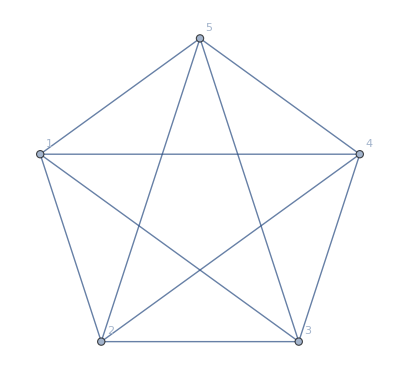

```mathematica
CompleteGraph[5,VertexLabels->Table[k->k,{k,1,5}]]
```

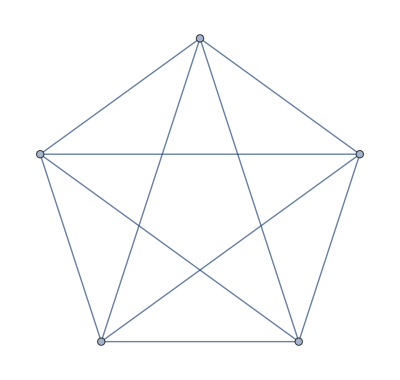

```mathematica
CompleteGraph[5,VertexLabels->Table[k->Placed[MySegment[k,5],Center],{k,1,5}]]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[CompleteGraph[4],allGraphs5[#,"graph"]]&]
```

{29525,29527,29533,29551,29605,29767,30253,31711,36085,49207}

```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[CompleteGraph[3],allGraphs4[#,"graph"]]&]
```

{365,367,373,391,445,607}

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[CompleteGraph[3],allGraphs5[#,"graph"]]&]//Length
```

25

```mathematica
allGraphs5NullAtomKeys
```

{0,39366,52974,57528,59048,54492,52976,43902,45416,43908,40878,40896,39384,39392,39372,39368,13122,17514,18980,17568,14586,14748,13284,13340,13176,13124,4374,5834,6320,4860,4920,4428,4380,1458,1944,2124,1620,1476,486,666,728,546,488,162,218,168,54,72,18,26,6,2}

```mathematica
k4InFivve=Sort[Select[Keys[allGraphs5],IsomorphicGraphQ[CompleteGraph[4],allGraphs5[#,"graph"]]&],CompareSymbols[allGraphs5[#1,"colofour"],allGraphs5[#2,"colofour"]]&]
```

{29525,29533,29527,29767,29605,29551,49207,36085,31711,30253}

```mathematica
TableForm[Total[Table[Map[If[#≠0,1,0]&,Vector5[k]],{k,k4InFivve}]],
TableHeadings->{ Table[Rotate[SymbolToLabel[allGraphs5[k,"colofourrealnull"]],Pi/2],{k,allGraphs5NullAtomKeysSorted}],None},
TableSpacing->{1, 0.3},TableDirections->Row
]
```

1|2|3|4|5 | 1|2|3|45 | 1|2|34|5 | 1|2|35|4 | 1|23|4|5 | 1|24|3|5 | 1|25|3|4 | 12|3|4|5 | 13|2|4|5 | 14|2|3|5 | 15|2|3|4 | 1|23|45 | 1|24|35 | 1|25|34 | 12|3|45 | 12|34|5 | 12|35|4 | 13|2|45 | 13|24|5 | 13|25|4 | 14|2|35 | 14|23|5 | 14|25|3 | 15|2|34 | 15|23|4 | 15|24|3 | 1|2|345 | 1|234|5 | 1|235|4 | 1|245|3 | 123|4|5 | 124|3|5 | 125|3|4 | 134|2|5 | 135|2|4 | 145|2|3 | 12|345 | 123|45 | 124|35 | 125|34 | 13|245 | 134|25 | 135|24 | 14|235 | 145|23 | 15|234 | 1|2345 | 1234|5 | 1235|4 | 1245|3 | 1345|2 | 12345
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 6 | 6 | 6 | 6 | 6 | 10

```mathematica
TableForm[Total[Drop[Table[Map[If[#≠0,1,0]&,Vector5[k]],{k,k4InFivve}],-5]],
TableHeadings->{ Table[Rotate[SymbolToLabel[allGraphs5[k,"colofourrealnull"]],Pi/2],{k,allGraphs5NullAtomKeysSorted}],None},
TableSpacing->{1, 0.3},TableDirections->Row
]
```

1|2|3|4|5 | 1|2|3|45 | 1|2|34|5 | 1|2|35|4 | 1|23|4|5 | 1|24|3|5 | 1|25|3|4 | 12|3|4|5 | 13|2|4|5 | 14|2|3|5 | 15|2|3|4 | 1|23|45 | 1|24|35 | 1|25|34 | 12|3|45 | 12|34|5 | 12|35|4 | 13|2|45 | 13|24|5 | 13|25|4 | 14|2|35 | 14|23|5 | 14|25|3 | 15|2|34 | 15|23|4 | 15|24|3 | 1|2|345 | 1|234|5 | 1|235|4 | 1|245|3 | 123|4|5 | 124|3|5 | 125|3|4 | 134|2|5 | 135|2|4 | 145|2|3 | 12|345 | 123|45 | 124|35 | 125|34 | 13|245 | 134|25 | 135|24 | 14|235 | 145|23 | 15|234 | 1|2345 | 1234|5 | 1235|4 | 1245|3 | 1345|2 | 12345
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 5 | 3 | 2 | 2 | 3 | 5

```mathematica
Total[Drop[Table[Vector5[k],{k,k4InFivve}],4]]
```

{0,0,0,0,0,1,1,1,1,1,1,0,-1,-1,-1,-1,-1,-1,-2,-2,-1,-1,-2,-1,-1,-2,0,-1,-1,-2,-2,-3,-3,-2,-2,-2,2,2,3,3,4,4,4,3,2,3,4,8,8,10,6,-36}

```mathematica
TableForm[Table[Vector5[k],{k,k4InFivve}],
TableHeadings->{Table[SymbolToLabel[allGraphs5[k,"colofour"]],{k,k4InFivve}], Table[Rotate[SymbolToLabel[allGraphs5[k,"colofourrealnull"]],Pi/2],{k,allGraphs5NullAtomKeysSorted}]},
TableSpacing->{1, 0.3}
]
```

| 1|2|3|4|5 | 1|2|3|45 | 1|2|34|5 | 1|2|35|4 | 1|23|4|5 | 1|24|3|5 | 1|25|3|4 | 12|3|4|5 | 13|2|4|5 | 14|2|3|5 | 15|2|3|4 | 1|23|45 | 1|24|35 | 1|25|34 | 12|3|45 | 12|34|5 | 12|35|4 | 13|2|45 | 13|24|5 | 13|25|4 | 14|2|35 | 14|23|5 | 14|25|3 | 15|2|34 | 15|23|4 | 15|24|3 | 1|2|345 | 1|234|5 | 1|235|4 | 1|245|3 | 123|4|5 | 124|3|5 | 125|3|4 | 134|2|5 | 135|2|4 | 145|2|3 | 12|345 | 123|45 | 124|35 | 125|34 | 13|245 | 134|25 | 135|24 | 14|235 | 145|23 | 15|234 | 1|2345 | 1234|5 | 1235|4 | 1245|3 | 1345|2 | 12345
1|2|3|45 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 2 | 2 | -6
1|2|34|5 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 2 | -6
1|2|35|4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | -6
1|23|4|5 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 0 | 0 | -6
1|24|3|5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 0 | 1 | 2 | 2 | 0 | 2 | 0 | -6
1|25|3|4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | -6
12|3|4|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | -6
13|2|4|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 2 | -6
14|2|3|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 0 | 2 | 0 | 2 | 2 | -6
15|2|3|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 2 | 2 | 2 | -6

```mathematica
Vector5
```

Vector5

```mathematica
k3InFivve=Sort[Select[Keys[allGraphs5],IsomorphicGraphQ[CompleteGraph[3],allGraphs5[#,"graph"]]&],CompareSymbols[allGraphs5[#1,"colofour"],allGraphs5[#2,"colofour"]]&]
```

{29768,29608,29560,49208,49216,49210,36086,36166,36112,31714,31954,31738,30262,30496,30334,29537,29857,29797,29633,56011,51475,49963,38281,36817,32441}

```mathematica
Total[Table[Vector5[k],{k,k3InFivve}]]
```

{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-7,-7,-7,-7,-7,50}

```mathematica
TableForm[Table[Vector5[k],{k,k3InFivve}],
TableHeadings->{Table[SymbolToLabel[allGraphs5[k,"colofour"]],{k,k3InFivve}], Table[Rotate[SymbolToLabel[allGraphs5[k,"colofourrealnull"]],Pi/2],{k,allGraphs5NullAtomKeysSorted}]},
TableSpacing->{1, 0.3}
]
```

| 1|2|3|4|5 | 1|2|3|45 | 1|2|34|5 | 1|2|35|4 | 1|23|4|5 | 1|24|3|5 | 1|25|3|4 | 12|3|4|5 | 13|2|4|5 | 14|2|3|5 | 15|2|3|4 | 1|23|45 | 1|24|35 | 1|25|34 | 12|3|45 | 12|34|5 | 12|35|4 | 13|2|45 | 13|24|5 | 13|25|4 | 14|2|35 | 14|23|5 | 14|25|3 | 15|2|34 | 15|23|4 | 15|24|3 | 1|2|345 | 1|234|5 | 1|235|4 | 1|245|3 | 123|4|5 | 124|3|5 | 125|3|4 | 134|2|5 | 135|2|4 | 145|2|3 | 12|345 | 123|45 | 124|35 | 125|34 | 13|245 | 134|25 | 135|24 | 14|235 | 145|23 | 15|234 | 1|2345 | 1234|5 | 1235|4 | 1245|3 | 1345|2 | 12345
1|23|45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 2
1|24|35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2
1|25|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2
12|3|45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2
12|34|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2
12|35|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2
13|2|45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
13|24|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2
13|25|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2
14|2|35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
14|23|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 2
14|25|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2
15|2|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 2
15|23|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 2
15|24|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 2
1|2|345 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 2
1|234|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 2
1|235|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 2
1|245|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 2
123|4|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 2
124|3|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 2
125|3|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 2
134|2|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 2
135|2|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 2
145|2|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 2

```mathematica
k2InFivve=Sort[Select[Keys[allGraphs5],IsomorphicGraphQ[CompleteGraph[2],allGraphs5[#,"graph"]]&],CompareSymbols[allGraphs5[#1,"colofour"],allGraphs5[#2,"colofour"]]&]
```

{49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014}

```mathematica
TableForm[Table[Vector5[k],{k,k2InFivve}],
TableHeadings->{Table[SymbolToLabel[allGraphs5[k,"colofour"]],{k,k2InFivve}], Table[Rotate[SymbolToLabel[allGraphs5[k,"colofourrealnull"]],Pi/2],{k,allGraphs5NullAtomKeysSorted}]},
TableSpacing->{1, 0.3}
]
```

| 1|2|3|4|5 | 1|2|3|45 | 1|2|34|5 | 1|2|35|4 | 1|23|4|5 | 1|24|3|5 | 1|25|3|4 | 12|3|4|5 | 13|2|4|5 | 14|2|3|5 | 15|2|3|4 | 1|23|45 | 1|24|35 | 1|25|34 | 12|3|45 | 12|34|5 | 12|35|4 | 13|2|45 | 13|24|5 | 13|25|4 | 14|2|35 | 14|23|5 | 14|25|3 | 15|2|34 | 15|23|4 | 15|24|3 | 1|2|345 | 1|234|5 | 1|235|4 | 1|245|3 | 123|4|5 | 124|3|5 | 125|3|4 | 134|2|5 | 135|2|4 | 145|2|3 | 12|345 | 123|45 | 124|35 | 125|34 | 13|245 | 134|25 | 135|24 | 14|235 | 145|23 | 15|234 | 1|2345 | 1234|5 | 1235|4 | 1245|3 | 1345|2 | 12345
12|345 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
123|45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
124|35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
125|34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
13|245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
134|25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
135|24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
14|235 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
145|23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
15|234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
1|2345 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
1234|5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
1235|4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
1245|3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
1345|2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1